## Javier Salazar 1001144647

## Project 11.

Choose your favorite stock [find its stock ticker symbol WXYZ, usually 1-4 letters].

(a) download the historical data of the stock for the period of 1 year
	I chose Disney - DIS.

(b) estimate the average return  μ and  volatility σ based on (a)

```mathematica
data={101.370003,100.800003,100.389999,100.349998,100.239998,102.169998,101.209999,100.889999,100.239998,100.150002,99.459999,101.150002,99.839996,99.230003,100.330002,100.059998,99.620003,98.760002,101.150002,102.480003,101.790001,99.970001,101.68,102.07,102.440002,102.919998,105.040001,104.339996,103.93,104.059998,104.07,102.889999,102.110001,102.199997,99.690002,99.980003,99.470001,99.360001,100.239998,99.940002,101.910004,102.470001,103.980003,104.349998,104.330002,106.309998,108.75,108.849998,107.059998,106.099998,107.150002,105.889999,106.339996,104.449997,104.260002,103.959999,104.769997,104.809998,105.330002,104.040001,105.339996,104.779999,106.019997,106.029999,108.040001,108.25,110,110.199997,110.300003,110.690002,112.129997,111.480003,111.089996,110.699997,111.18,113.510002,112.620003,112.629997,113.559998,112.970001,112.75,114.089996,115.940002,116.559998,113.980003,114.160004,112.68,112.120003,112.75,112.849998,112.480003,112.480003,111.989998,112.389999,111.940002,112,111.93,112.330002,112.580002,112.449997,111.919998,112.019997,110.849998,109.870003,110.260002,110.970001,110.68,109.599998,109.459999,110.669998,109.260002,109.360001,109.529999,109.790001,111.620003,110.400002,112.769997,113.629997,115.209999,116.040001,116.940002,116.239998,117.660004,116.910004,116.129997,114.779999,116.019997,116.889999,112.860001,111.150002,112.610001,113.440002,116.190002,117.129997,116.18,118.900002,118.269997,117.849998,111.610001,114.160004,113.190002,113.040001,114.760002,114.830002,116.099998,115.18,115.449997,116.709999,117.050003,116,118,116.699997,116.849998,117.120003,117.110001,116.190002,115.419998,111.870003,113.029999,112.080002,112.550003,113.900002,116.099998,116.610001,115.489998,115.739998,112.870003,114.330002,111.980003,111.860001,111.970001,112.209999,113.389999,112.199997,110.620003,109.449997,109.220001,107,104.220001,100.349998,105.830002,106.519997,107.300003,109.650002,108.970001,106.330002,109.610001,110.559998,111.419998,112.669998,112.800003,112.650002,112.419998,111.760002,110.910004,111.010002,111.040001,110.599998,111.120003,110.550003,111.089996,110.809998,110.900002,110.129997,111.519997,111.300003,111.800003,112.660004,111.410004,110.949997,111.510002,109.440002,109.199997,110.199997,110.660004,112.589996,113.510002,113.68,114.290001,115.25,113.589996,113.5,112.779999,112.839996,114.010002,114.330002,114,114.849998,114.010002,113.809998,114.75,114.730003,114.089996,114.480003,114.959999,113.120003,110,109.989998,108.660004,108.230003,107.790001,110.139999,110.279999,110.709999,111.029999,112.510002,111.959999,112.519997,114.75,115,114.959999,116.860001,116.559998};
```

```mathematica
Length[data]
```

253

```mathematica
dat2=Table[Log[data[[k]]/data[[k-1]]],{k,2,Length[data]}]//N;
```

```mathematica
Mean[dat2]
```

0.000554083

```mathematica
StandardDeviation[dat2]
```

0.0119835

```mathematica
253Mean[dat2] (* estimate of  μ -1/2 σ^2 *)
```

0.140183

```mathematica
0.1401830087781906
(* estimate of  μ - 1/2 σ^2  ~ annual return of 14.0 % *)
```

```mathematica
√253 StandardDeviation[dat2]//N (* estimate of σ *)
```

0.190609

```mathematica
0.1906093224148171
(* estimate of σ  ~ annual volatility of 19.1 % *)
```

```mathematica
0.1401830087781906+1/2(0.1906093224148171 )^2
```

0.158349

```mathematica
(* estimate of μ  ~ annual return of 15 % *)
```

(c) simulate hypothetical future stock  with μ and σ found in (b)  for the period of 6 months 
     and show the graphs of 3 different

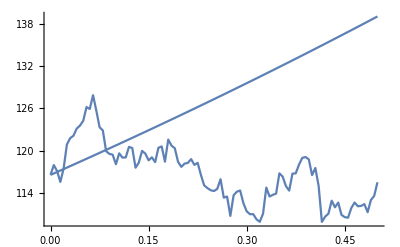

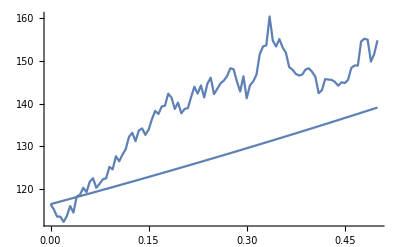

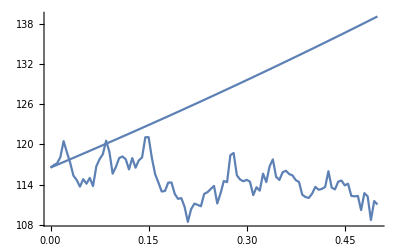

```mathematica
BrownianGeometric[x0_,μ_,σ_,t_,h_]:=Module[{d=√h,m=t/h},
g=Table[Random[NormalDistribution[0,d]],{m}];
sums=FoldList[Plus,0,g];Table[X[i*h]=sums[[i+1]],{i,0,m}];
geometric=Table[{i*h,x0*ⅇ^(μ *i/m+σ*X[i*h])},{i,0,m}];
drift=Table[{i*h,x0*ⅇ^((i/m) * (μ +σ^2/2))},{i,0,m}];
g1=ListPlot[geometric,Joined->True,DisplayFunction->Identity];
g2=ListPlot[drift,Joined->True,DisplayFunction->Identity];
Show[g1,g2,PlotRange->All,DisplayFunction->$DisplayFunction]];
BrownianGeometric[116.559998,.15834896567390844,0.1906093224148171,.5,.005]
BrownianGeometric[116.559998,.15834896567390844,0.1906093224148171,.5,.005]
BrownianGeometric[116.559998,.15834896567390844,0.1906093224148171,.5,.005]
```

(d) choose a strike price K for Call Option with 6 months expiration time [measured in year units, i.e.,  months = 6/12]
	Choosing strike price K = $115

(e) choose risk free rate r [in decimal percentage, i.e. 2% means to .02] and use the Black-Scholes formula to find the
     present value of your option.  Specify the source and type of r used (e.g, treasury, CD, money market, LIBOR, etc)
     	Choosing r = 2.46% from US Treasury

```mathematica
Φ[x_]:=CDF[NormalDistribution[0,1],x];
```

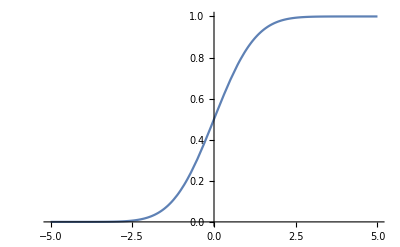

```mathematica
Plot[Φ[x],{x,-5,5}]
```

```mathematica
OptionVal[t_,T_,Xt_,K_,σ_,r_]:=
Xt*Φ[((r+σ^2/2)*(T-t)+Log[Xt/K])/(σ √(T-t))]-K ⅇ^(-r*(T-t))*Φ[((r-σ^2/2)*(T-t)+Log[Xt/K])/(σ √(T-t))];
```

```mathematica
OptionVal[0,1/2,116.559998,115,0.1906093224148171,.0246]
```

7.77845

(f) compare your option value computed from the Black-Scholes Formula with the option value listed at CBOE
     website [your answer should be close to the CBOE trading price]
     	The option value listed at the CBOE website is 8.8 which is close to my calculated option value.

*For any given Strike Price, generally one chooses the last listed trade [i.e., if the underlying Call Option is
 currently/actively traded and falls between the bid- ask price range. If the last trade listing is out of  bid-ask range
 [i.e., it means that last trade is an old data], then use the average of the bid and ask price as Call Option price.
     
(g) tweak with σ in the B-S formula [by trial and error]  to match the CBOE price exactly.

```mathematica
OptionVal[0,1/2,116.559998,115,0.2227,.0246]
```

8.8012

The adjusted volatility is 0.2227 which is slightly higher than the volatility calculated using the past years stock data for Disney.